#### Get component function (temporary)

```mathematica
Needs["Olveretal`"];
ClearAll[GetComponent]
Options[GetComponent]={Coordinates->"Spherical",Mute->True};
GetComponent[solvec_List,expr_List,layer_Integer,layout_List,n_Integer,OptionsPattern[]]:=
Block[{position,subdomain,nsubdomains,partition,zeroInDomain,startindex,listParity,listExtracted,(*options*) coordinates},

(* set up options *)
coordinates=OptionValue[Coordinates];
If[!OptionValue[Mute],
If[SameQ[coordinates,"Spheroidal"],Print["Spheroidal coordinates"],Print["Spherical coordinates"]]
];

(* recover subdomains from model *)
partition=Partition[Sort(*@Rest*)[Sprouts`domain],2,1];
nsubdomains=Length[partition];
Table[subdomain[i]=partition⟦i⟧,{i,1,Length[partition]}];
If[SameQ[N@First[subdomain[1]],0.],zeroInDomain=True,zeroInDomain=False];

(* find component position in solution vector *)
position=Flatten@Position[layout,Alternatives@@expr];

(* find parity of fields accross the origin based on their indices of spherical harmonics *)
listParity=
Block[{out},
If[zeroInDomain&&SameQ[layer,1],
Which[
SameQ[coordinates,"Spheroidal"],
Which[
MatchQ[#,f_[ℓ_,𝓂_]/;EvenQ[ℓ+𝓂]],out="even";,
MatchQ[#,f_[ℓ_,𝓂_]/;OddQ[ℓ+𝓂]],out="odd";,
True,Print["error with parity !"]
],
SameQ[coordinates,"Spherical"],
Which[
MatchQ[#,f_[ℓ_,𝓂_]/;EvenQ[ℓ]],out="even";,
MatchQ[#,f_[ℓ_,𝓂_]/;OddQ[ℓ]],out="odd";,
True,Print["error with parity !"];
],
True,Print["error with coordinates !"];
]
];
out
]&/@expr;

(* extracted elements from solution vector *)
listExtracted=
Block[{extracted},
If[zeroInDomain,
startindex=Max[(layer-3/2)*n*Length[layout]+1,1];
If[SameQ[layer,1],
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n/2-1⟧,{(#-1)*n/2+1,#*n/2}],
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n-1⟧,{(#-1)*n+1,#*n}]
],
startindex=(layer-1)*n*Length[layout]+1;
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n-1⟧,{(#-1)*n+1,#*n}]
]
]&/@position;

(* output: riffle with zeroes if zero is in first layer *)
If[zeroInDomain&&SameQ[layer,1],
Table[
Switch[listParity⟦i⟧,
"even",N@Riffle[listExtracted⟦i⟧,0.+0.ⅈ],
"odd",N@Riffle[listExtracted⟦i⟧,0.+0.ⅈ,{1,-1,2}],
True,Print["error with Riffle !"]
]
,{i,1,Length[expr]}],
N@listExtracted
]

]
```

Get::noopen: Cannot open Olveretal`.

Needs::nocont: Context Olveretal` was not created when Needs was evaluated.

# Topographic forcing

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["TenGSHui`","~/ownCloud/Shared/TenGSHui.m"];
Needs["spectral`","../spectral.m"];
Needs["sprouts`","../sprouts.m"];
```

Loading TenGSHui...

Done. Please execute DisplayPalette if you need the palette.

```mathematica
FastMode=True;
```

```mathematica
ℓmax=12;𝓂=2;ricb=0.35;
```

```mathematica
Rank[𝕦]^=1;
MaxDegree[𝕦]^=ℓmax+1;
𝕦[-1][ℓ_,𝓂_][r_]:=√((ℓ(ℓ+1))/2)((P[ℓ,𝓂][r])/r+P[ℓ,𝓂]'[r]-ⅈ T[ℓ,𝓂][r])
𝕦[0][ℓ_,𝓂_][r_]:=ℓ(ℓ+1)(P[ℓ,𝓂][r])/r
𝕦[1][ℓ_,𝓂_][r_]:=√((ℓ(ℓ+1))/2)((P[ℓ,𝓂][r])/r+P[ℓ,𝓂]'[r]+ⅈ T[ℓ,𝓂][r])
```

```mathematica
Rank[𝕓]^=1;
MaxDegree[𝕓]^=ℓmax+1;
𝕓[-1][ℓ_,𝓂_][r_]:=√((ℓ(ℓ+1))/2)((F[ℓ,𝓂][r])/r+F[ℓ,𝓂]'[r]-ⅈ G[ℓ,𝓂][r])
𝕓[0][ℓ_,𝓂_][r_]:=ℓ(ℓ+1)(F[ℓ,𝓂][r])/r
𝕓[1][ℓ_,𝓂_][r_]:=√((ℓ(ℓ+1))/2)((F[ℓ,𝓂][r])/r+F[ℓ,𝓂]'[r]+ⅈ G[ℓ,𝓂][r])
```

```mathematica
viscosity≐𝕦
```

```mathematica
Rank[δ𝒯]^=0;
MaxDegree[δ𝒯]^=ℓmax+1;
δ𝒯[][ℓ_,𝓂_][r_]:=δT[ℓ,𝓂][r]
```

```mathematica
buoy≐δ𝒯⊗𝕣
```

```mathematica
ClearAll[𝒯0]
rc=0.7;h=0.1;
Rank[𝒯0]^=0;
MaxDegree[𝒯0]^=0;
𝒯0[][0,0][r_]:=1/4 (2 r+h Log[Cosh[(2 (r-rc))/h]])
```

```mathematica
𝕧≐ω⋆(𝟙[𝕫]𝕣)
```

```mathematica
𝔹0≐√3⋆𝟙[𝕫]
```

```mathematica
$n=0;
Rank[ε]^=0;
MaxDegree[ε]^=0;
ε[][0,0][q_]:=0
```

```mathematica
(((𝔹0·𝕖𝓇)⊗(𝔹0·𝕖𝓇))⊗𝕖𝓇)1ε==4π
```

True

```mathematica
lorentz≐(𝕓)𝔹0
```

```mathematica
listpoleq=Table[Simplify[(((ⅈ ω)⋆𝕦)⊕2⋆(𝟙[𝕫]𝕦)⊕Ek⋆viscosity⊕N02⋆buoy⊕Le2⋆lorentz)[0][ℓ,𝓂][r]],{ℓ,2,ℓmax,2}];
listtoreq=Table[Simplify[(((ⅈ ω)⋆𝕦)⊕2⋆(𝟙[𝕫]𝕦)⊕Ek⋆viscosity⊕N02⋆buoy⊕Le2⋆lorentz)[0][ℓ,𝓂][r]],{ℓ,Abs[𝓂]+1,ℓmax+2,2}];
listpolmageq=Table[Simplify[(((ⅈ ω)⋆𝕓)⊕(𝕦𝔹0)⊕Em⋆𝕓)[0][ℓ,𝓂][r]],{ℓ,Abs[𝓂]+1,ℓmax+2,2}];
listtormageq=Table[Simplify[(((ⅈ ω)⋆𝕓)⊕(𝕦𝔹0)⊕Em⋆𝕓)[0][ℓ,𝓂][r]],{ℓ,2,ℓmax,2}];
listthermaleq=Table[Simplify[(((ⅈ ω)⋆δ𝒯)⊕(𝒯0𝕦)⊕-Ek/Pr⋆(∇δ𝒯))[][ℓ,𝓂][r]],{ℓ,2,ℓmax,2}];
```

```mathematica
listpol=Table[P[ℓ,𝓂],{ℓ,2,ℓmax,2}];
listtor=Table[T[ℓ,𝓂],{ℓ,Abs[𝓂]+1,ℓmax+2,2}];
listpolmag=Table[F[ℓ,𝓂],{ℓ,Abs[𝓂]+1,ℓmax+2,2}];
listtormag=Table[G[ℓ,𝓂],{ℓ,2,ℓmax,2}];
listthermal=Table[δT[ℓ,𝓂],{ℓ,2,ℓmax,2}];
```

```mathematica
ClearAll[listpolbc,listtorbc,listthermalbc]
If[ricb==0,
listpolbc=Flatten[Table[{P[ℓ,𝓂][1],P[ℓ,𝓂]''[1]},{ℓ,2,ℓmax,2}]];
listtorbc=Flatten[Table[{T[ℓ,𝓂]'[1]-T[ℓ,𝓂][1]},{ℓ,Abs[𝓂]+1,ℓmax+2,2}]];
listthermalbc=Flatten[Table[{δT[ℓ,𝓂][1]},{ℓ,2,ℓmax,2}]];
,
listpolbc=Flatten[Table[{P[ℓ,𝓂][ricb],P[ℓ,𝓂]'[ricb]+(P[ℓ,𝓂][ricb])/ricb,P[ℓ,𝓂]''[1]-(2-ℓ(ℓ+1))P[ℓ,𝓂][1],(*P[ℓ,𝓂]'[1]+P[ℓ,𝓂][1],*)P[ℓ,𝓂][1]+ⅈ/(ℓ(ℓ+1)) ω ϵ KroneckerDelta[ℓ,2]},{ℓ,2,ℓmax,2}]];
listpolmagbc=Flatten[Table[{F[ℓ,𝓂]'[ricb]-ℓ (F[ℓ,𝓂][ricb])/ricb,F[ℓ,𝓂]'[1]+(ℓ+1) F[ℓ,𝓂][1]},{ℓ,Abs[𝓂]+1,ℓmax+2,2}]];
listtormagbc=Flatten[Table[{G[ℓ,𝓂][ricb],G[ℓ,𝓂][1]},{ℓ,2,ℓmax,2}]];
listtorbc=Flatten[Table[{T[ℓ,𝓂][ricb],T[ℓ,𝓂]'[1]-T[ℓ,𝓂][1]},{ℓ,Abs[𝓂]+1,ℓmax+2,2}]];
listthermalbc=Flatten[Table[{δT[ℓ,𝓂][ricb],δT[ℓ,𝓂][1]},{ℓ,2,ℓmax,2}]];
];
```

```mathematica
ℒ=Join[listpoleq,listtoreq,listpolmageq,listtormageq,listthermaleq];
𝒱=Join[listpol,listtor,listpolmag,listtormag,listthermal];
ℬ=Join[listpolbc,listtorbc,listpolmagbc,listtormagbc,listthermalbc];
```

```mathematica
Block[{Ek=10^-3,N02=100,Pr=1,ω=𝓂 1,Le2=1,Em=10^-3,ϵ=10^-4},
A=SproutsFun[Join[ℒ,ℬ],𝒱,{r,ricb,1},48]
]
```

partition of the spatial domain :  {{0.35,1}}

linear problem of the type Ax=b

Size of output matrices :  1440x1440

{SparseArray[…],SparseArray[<68089>, {1440, 1440}]}

```mathematica
Export["~/Desktop/A.mtx",A[[2]]]
Export["~/Desktop/b.mtx",{Normal[A[[1]]]}]
```

~/Desktop/A.mtx

~/Desktop/b.mtx

## Solve and post-process

```mathematica
sol=LinearSolve[A[[2]],A[[1]]];
```

```mathematica
(* extract components from solution *)
ClearAll[out,outnull]
Block[{list,coef,assoc=<||>},
Table[
list[layer]=Sprouts`layout⟦layer⟧;
coef[layer]=Chop@GetComponent[sol,list[layer],layer,Sprouts`layout⟦layer⟧,Sprouts`nr];
AppendTo[assoc,AssociationThread[list[layer],coef[layer]]]
,{layer,1,Sprouts`nlayers}];
out=assoc;
]
outnull=Map[(#)->ConstantArray[0,Sprouts`nr]&,Keys[out]/.f_[ℓ_,𝓂_]->f[ℓ-1,𝓂]]~Join~Map[(#)->ConstantArray[0,Sprouts`nr]&,Keys[out]/.f_[ℓ_,𝓂_]->f[ℓ+1,𝓂]];
AppendTo[out,outnull];
```

```mathematica
ClearAll[NChebevalC]
NChebevalC[c_][x_]:=NChebeval[N[Re[c]]][x]+ⅈ NChebeval[N[Im[c]]][x]
xk=Join[{1},Cos[((2Range[1,Sprouts`nr]-1)π)/(2Sprouts`nr)],{-1}]//N;
rk=Sprouts`rfu[1][xk];
```

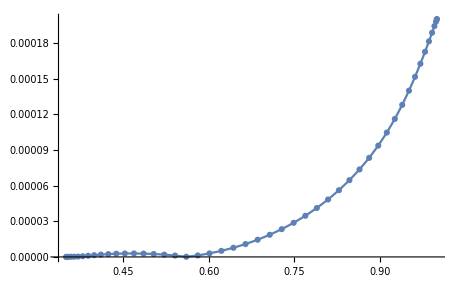

```mathematica
(* plot chosen component *)
With[{ℓ=2,𝓂=2},
data=ℓ(ℓ+1)(NChebevalC[P[ℓ,𝓂]/.out][xk])/rk;
ListPlot[{{rk,Abs[data]}ᵀ},Joined->True,PlotMarkers->Automatic]
]
```

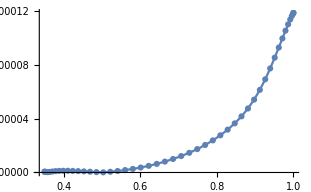

```mathematica
(* plot chosen component *)
With[{ℓ=2,𝓂=2},
data=NChebevalC[DCheb[P[ℓ,𝓂]/.out]][xk]+(NChebevalC[P[ℓ,𝓂]/.out][xk])/rk;
ListPlot[{{rk,Abs[data]}ᵀ},Joined->True,PlotMarkers->Automatic,PlotRange->All]
]
```

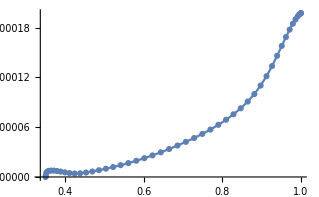

```mathematica
(* plot chosen component *)
With[{ℓ=3,𝓂=2},
data=NChebevalC[T[ℓ,𝓂]/.out][xk];
ListPlot[{{rk,Abs[data]}ᵀ},Joined->True,PlotMarkers->Automatic]
]
```

```mathematica
NChebevalC[DCheb[P[2,2]/.out]][1]
NChebevalC[P[2,2]/.out][1]
```

-7.46786×10^-6-0.0000848769 ⅈ

-9.17493×10^-11-0.000033334 ⅈ

```mathematica
Block[{ℓ=2,ω=1},
ε[ℓ,𝓂]=10^-4;
ε[ℓ_,𝓂_]=0;
Plmck=(P[ℓ,𝓂]/.out);
Tlp1mck=(T[ℓ+1,𝓂]/.out);
Tlm1mck=(T[ℓ-1,𝓂]/.out);
tabT=Table[ChebyshevT[k,x]/.x->1,{k,0,Length[Plmck]-1}];
tabTp=Table[D[ChebyshevT[k,x],{x,1}]/.x->1,{k,0,Length[Plmck]-1}];

Slmcmb=Plmck.tabT+Plmck.tabTp;
Tlp1mcmb=Tlp1mck.tabT;
Tlm1mcmb=Tlm1mck.tabT;

2Re[ⅈ ω((*ⅈ 𝓂 Slmcmb*)+(ℓ+2)/(2ℓ+3)√((ℓ+𝓂+1)(ℓ-𝓂+1))Tlp1mcmb-(ℓ-1)/(2ℓ-1)√((ℓ+𝓂)(ℓ-𝓂))Tlm1mcmb)ε[ℓ,𝓂]*]
]
```

4.27635×10^-9

{0.220277,0,0.575761,0,0.631366,0,-0.555484,0,0.148357,0,-0.0202769}

0.-34.5505 x+133.006 x^3-140.845 x^5+51.9089 x^7+x (-4.7683+121.243 x^2-329.946 x^4+307.645 x^6-103.818 x^8)

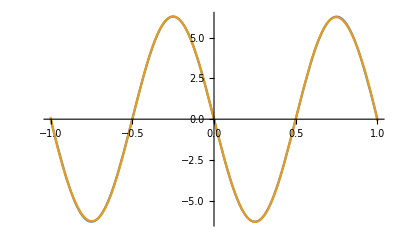

```mathematica
NChebckf[Cos[2π x],x,10]
Chebeval[DCheb[%]][x]
Plot[{-2π Sin[2π x],%},{x,-1,1}]
```

```mathematica
(*Export["~/Desktop/Qlm.txt",Abs[6(NChebevalC[P[2,2]/.out][xk])/rk]]*)
```

~/Desktop/Qlm.txt

```mathematica
(*Export["~/Desktop/rk.txt",rk]*)
```

~/Desktop/rk.txt

```mathematica
ClearAll[up,ut,upint,utint,urint,ucint,upintconj,ucintconj,urintconj,utintconj,uout]
ClearAll[bp,bt,bpint,btint,brint,bcint,bpintconj,bcintconj,brintconj,btintconj,bout]
gridr=N@Subdivide[Sequence@@Sprouts`layer[1],100];
Block[{mode=pos,ℓ,𝓂,head,subset=Sprouts`layout⟦1⟧,listcomp,comp},
listcomp=GetComponent[sol,subset,1,Sprouts`layout⟦1⟧,Sprouts`nr,Coordinates->"Spherical"];
Table[
head=Head[subset⟦i⟧];ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
comp=listcomp⟦i⟧;
Which[
SameQ[head,P],
up[ℓ,𝓂]=((Function[x,(NChebeval[Re@N@#][Sprouts`ufr[1][x]]+ⅈ NChebeval[N@Im@#][Sprouts`ufr[1][x]])]/@gridr)&@comp);
upint[ℓ,𝓂]=Interpolation[{gridr,up[ℓ,𝓂]}ᵀ];
upintconj[ℓ,𝓂]=Interpolation[{gridr,up[ℓ,𝓂]*}ᵀ];
urint[ℓ,𝓂]=Evaluate[(ℓ(ℓ+1))/# upint[ℓ,𝓂][#]]&;
urintconj[ℓ,𝓂]=Evaluate[(ℓ(ℓ+1))/# upintconj[ℓ,𝓂][#]]&;
ucint[ℓ,𝓂]=Evaluate[(upint[ℓ,𝓂][#])/#+upint[ℓ,𝓂]'[#]]&;
ucintconj[ℓ,𝓂]=Evaluate[(upintconj[ℓ,𝓂][#])/#+upintconj[ℓ,𝓂]'[#]]&,
SameQ[head,T],
ut[ℓ,𝓂]=((Function[x,(NChebeval[Re@N@#][Sprouts`ufr[1][x]]+ⅈ NChebeval[N@Im@#][Sprouts`ufr[1][x]])]/@gridr)&@comp);
utint[ℓ,𝓂]=Interpolation[{gridr,ut[ℓ,𝓂]}ᵀ];
utintconj[ℓ,𝓂]=Interpolation[{gridr,ut[ℓ,𝓂]*}ᵀ],
SameQ[head,F],
bp[ℓ,𝓂]=((Function[x,(NChebeval[Re@N@#][Sprouts`ufr[1][x]]+ⅈ NChebeval[N@Im@#][Sprouts`ufr[1][x]])]/@gridr)&@comp);
bpint[ℓ,𝓂]=Interpolation[{gridr,bp[ℓ,𝓂]}ᵀ];
bpintconj[ℓ,𝓂]=Interpolation[{gridr,bp[ℓ,𝓂]*}ᵀ];
brint[ℓ,𝓂]=Evaluate[(ℓ(ℓ+1))/# bpint[ℓ,𝓂][#]]&;
brintconj[ℓ,𝓂]=Evaluate[(ℓ(ℓ+1))/# bpintconj[ℓ,𝓂][#]]&;
bcint[ℓ,𝓂]=Evaluate[(bpint[ℓ,𝓂][#])/#+bpint[ℓ,𝓂]'[#]]&;
bcintconj[ℓ,𝓂]=Evaluate[(bpintconj[ℓ,𝓂][#])/#+bpintconj[ℓ,𝓂]'[#]]&,
SameQ[head,G],
bt[ℓ,𝓂]=((Function[x,(NChebeval[Re@N@#][Sprouts`ufr[1][x]]+ⅈ NChebeval[N@Im@#][Sprouts`ufr[1][x]])]/@gridr)&@comp);
btint[ℓ,𝓂]=Interpolation[{gridr,bt[ℓ,𝓂]}ᵀ];
btintconj[ℓ,𝓂]=Interpolation[{gridr,bt[ℓ,𝓂]*}ᵀ]
];
uout[-1][ℓ,𝓂]=Evaluate[√((ℓ(ℓ+1))/2)(ucint[ℓ,𝓂][#]-ⅈ utint[ℓ,𝓂][#])]&;uout[0][ℓ,𝓂]=Evaluate[urint[ℓ,𝓂][#]]&;uout[+1][ℓ,𝓂]=Evaluate[√((ℓ(ℓ+1))/2)(ucint[ℓ,𝓂][#]+ⅈ utint[ℓ,𝓂][#])]&;
bout[-1][ℓ,𝓂]=Evaluate[√((ℓ(ℓ+1))/2)(bcint[ℓ,𝓂][#]-ⅈ btint[ℓ,𝓂][#])]&;bout[0][ℓ,𝓂]=Evaluate[brint[ℓ,𝓂][#]]&;bout[+1][ℓ,𝓂]=Evaluate[√((ℓ(ℓ+1))/2)(bcint[ℓ,𝓂][#]+ⅈ btint[ℓ,𝓂][#])]&;

,{i,1,Length[subset]}]
];
```

```mathematica
utint[ℓ_,𝓂_][r_]:=0;
urint[ℓ_,𝓂_][r_]:=0;
ucint[ℓ_,𝓂_][r_]:=0;
upint[ℓ_,𝓂_][r_]:=0;
utintconj[ℓ_,𝓂_][r_]:=0;
urintconj[ℓ_,𝓂_][r_]:=0;
ucintconj[ℓ_,𝓂_][r_]:=0;
upintconj[ℓ_,𝓂_][r_]:=0;
btint[ℓ_,𝓂_][r_]:=0;
brint[ℓ_,𝓂_][r_]:=0;
bcint[ℓ_,𝓂_][r_]:=0;
bpint[ℓ_,𝓂_][r_]:=0;
btintconj[ℓ_,𝓂_][r_]:=0;
brintconj[ℓ_,𝓂_][r_]:=0;
bcintconj[ℓ_,𝓂_][r_]:=0;
bpintconj[ℓ_,𝓂_][r_]:=0;
```

```mathematica
<<MaTeX`
```

```mathematica
ClearAll[rxgradY,rgradY,Y]
Y[ℓ_,𝓂_,θ_,ϕ_]:=Y[ℓ,𝓂,θ,ϕ]=√((4π)/(1+2 ℓ))SphericalHarmonicY[ℓ,𝓂,θ,ϕ]
rgradY[ℓ_,𝓂_,θ_,ϕ_]:=rgradY[ℓ,𝓂,θ,ϕ]={0,𝓂 Cot[θ] Y[ℓ,𝓂,θ,ϕ]+(ⅇ^(-ⅈ ϕ) √((1+ℓ-𝓂)!) √((2+ℓ+𝓂)!))/(√((ℓ-𝓂)!) √((1+ℓ+𝓂)!)) Y[ℓ,1+𝓂,θ,ϕ],ⅈ 𝓂 Csc[θ] Y[ℓ,𝓂,θ,ϕ]}
rxgradY[ℓ_,𝓂_,θ_,ϕ_]:=rxgradY[ℓ,𝓂,θ,ϕ]={0,-ⅈ 𝓂 Csc[θ] Y[ℓ,𝓂,θ,ϕ],𝓂 Cot[θ] Y[ℓ,𝓂,θ,ϕ]+(ⅇ^(-ⅈ ϕ)  √((1+ℓ-𝓂)!) √((2+ℓ+𝓂)!))/(√((ℓ-𝓂)!) √((1+ℓ+𝓂)!))Y[ℓ,1+𝓂,θ,ϕ]}
```

```mathematica
ℓmin=2;
```

```mathematica
ClearAll[upol,utor,ur,uθ,uϕ]
upol[r_,θ_,ϕ_]:=upol[r,θ,ϕ]=2(If[Mod[𝓂,2]==0,
Sum[Re@(upint[ℓ,𝓂][r]Y[ℓ,𝓂,θ,ϕ]),{ℓ,ℓmin,ℓmax}],
Sum[Im@(upint[ℓ,𝓂][r]Y[ℓ,𝓂,θ,ϕ]),{ℓ,ℓmin,ℓmax}]
]);
utor[r_,θ_,ϕ_]:=utor[r,θ,ϕ]=2(If[Mod[𝓂,2]==0,
Sum[Re@(utint[ℓ,𝓂][r]Y[ℓ,𝓂,θ,ϕ]),{ℓ,ℓmin,ℓmax}],
Sum[Im@(utint[ℓ,𝓂][r]Y[ℓ,𝓂,θ,ϕ]),{ℓ,ℓmin,ℓmax}]
]);
ur[r_,θ_,ϕ_]:=ur[r,θ,ϕ]=2(If[Mod[𝓂,2]==0,
Sum[Re@(urint[ℓ,𝓂][r]Y[ℓ,𝓂,θ,ϕ]{1,0,0})+Im@((ucint[ℓ,𝓂][r]rgradY[ℓ,𝓂,θ,ϕ])-(utint[ℓ,𝓂][r]rxgradY[ℓ,𝓂,θ,ϕ])),{ℓ,ℓmin,ℓmax}],
Sum[Im@(urint[ℓ,𝓂][r]Y[ℓ,𝓂,θ,ϕ]{1,0,0})+Re@((ucint[ℓ,𝓂][r]rgradY[ℓ,𝓂,θ,ϕ])-(utint[ℓ,𝓂][r]rxgradY[ℓ,𝓂,θ,ϕ])),{ℓ,ℓmin,ℓmax}]
])⟦1⟧
uθ[r_,θ_,ϕ_]:=uθ[r,θ,ϕ]=2(If[Mod[𝓂,2]==0,
Sum[Re@(urint[ℓ,𝓂][r]Y[ℓ,𝓂,θ,ϕ]{1,0,0})+Im@((ucint[ℓ,𝓂][r]rgradY[ℓ,𝓂,θ,ϕ])-(utint[ℓ,𝓂][r]rxgradY[ℓ,𝓂,θ,ϕ])),{ℓ,ℓmin,ℓmax}],
Sum[Im@(urint[ℓ,𝓂][r]Y[ℓ,𝓂,θ,ϕ]{1,0,0})+Re@((ucint[ℓ,𝓂][r]rgradY[ℓ,𝓂,θ,ϕ])-(utint[ℓ,𝓂][r]rxgradY[ℓ,𝓂,θ,ϕ])),{ℓ,ℓmin,ℓmax}]
])⟦2⟧
uϕ[r_,θ_,ϕ_]:=uϕ[r,θ,ϕ]=2(If[Mod[𝓂,2]==0,
Sum[Re@(urint[ℓ,𝓂][r]Y[ℓ,𝓂,θ,ϕ]{1,0,0})+Im@((ucint[ℓ,𝓂][r]rgradY[ℓ,𝓂,θ,ϕ])-(utint[ℓ,𝓂][r]rxgradY[ℓ,𝓂,θ,ϕ])),{ℓ,ℓmin,ℓmax}],
Sum[Im@(urint[ℓ,𝓂][r]Y[ℓ,𝓂,θ,ϕ]{1,0,0})+Re@((ucint[ℓ,𝓂][r]rgradY[ℓ,𝓂,θ,ϕ])-(utint[ℓ,𝓂][r]rxgradY[ℓ,𝓂,θ,ϕ])),{ℓ,ℓmin,ℓmax}]
])⟦3⟧
```

```mathematica
ClearAll[bpol,btor,br,bθ,bϕ]
bpol[r_,θ_,ϕ_]:=upol[r,θ,ϕ]=2(If[Mod[𝓂,2]==0,
Sum[Re@(bpint[ℓ,𝓂][r]Y[ℓ,𝓂,θ,ϕ]),{ℓ,ℓmin,ℓmax}],
Sum[Im@(bpint[ℓ,𝓂][r]Y[ℓ,𝓂,θ,ϕ]),{ℓ,ℓmin,ℓmax}]
]);
btor[r_,θ_,ϕ_]:=utor[r,θ,ϕ]=2(If[Mod[𝓂,2]==0,
Sum[Re@(btint[ℓ,𝓂][r]Y[ℓ,𝓂,θ,ϕ]),{ℓ,ℓmin,ℓmax}],
Sum[Im@(btint[ℓ,𝓂][r]Y[ℓ,𝓂,θ,ϕ]),{ℓ,ℓmin,ℓmax}]
]);
br[r_,θ_,ϕ_]:=br[r,θ,ϕ]=2(If[Mod[𝓂,2]==0,
Sum[Re@(brint[ℓ,𝓂][r]Y[ℓ,𝓂,θ,ϕ]{1,0,0})+Im@((bcint[ℓ,𝓂][r]rgradY[ℓ,𝓂,θ,ϕ])-(btint[ℓ,𝓂][r]rxgradY[ℓ,𝓂,θ,ϕ])),{ℓ,ℓmin,ℓmax}],
Sum[Im@(brint[ℓ,𝓂][r]Y[ℓ,𝓂,θ,ϕ]{1,0,0})+Re@((bcint[ℓ,𝓂][r]rgradY[ℓ,𝓂,θ,ϕ])-(btint[ℓ,𝓂][r]rxgradY[ℓ,𝓂,θ,ϕ])),{ℓ,ℓmin,ℓmax}]
])⟦1⟧
bθ[r_,θ_,ϕ_]:=bθ[r,θ,ϕ]=2(If[Mod[𝓂,2]==0,
Sum[Re@(brint[ℓ,𝓂][r]Y[ℓ,𝓂,θ,ϕ]{1,0,0})+Im@((bcint[ℓ,𝓂][r]rgradY[ℓ,𝓂,θ,ϕ])-(btint[ℓ,𝓂][r]rxgradY[ℓ,𝓂,θ,ϕ])),{ℓ,ℓmin,ℓmax}],
Sum[Im@(brint[ℓ,𝓂][r]Y[ℓ,𝓂,θ,ϕ]{1,0,0})+Re@((bcint[ℓ,𝓂][r]rgradY[ℓ,𝓂,θ,ϕ])-(btint[ℓ,𝓂][r]rxgradY[ℓ,𝓂,θ,ϕ])),{ℓ,ℓmin,ℓmax}]
])⟦2⟧
bϕ[r_,θ_,ϕ_]:=bϕ[r,θ,ϕ]=2(If[Mod[𝓂,2]==0,
Sum[Re@(brint[ℓ,𝓂][r]Y[ℓ,𝓂,θ,ϕ]{1,0,0})+Im@((bcint[ℓ,𝓂][r]rgradY[ℓ,𝓂,θ,ϕ])-(btint[ℓ,𝓂][r]rxgradY[ℓ,𝓂,θ,ϕ])),{ℓ,ℓmin,ℓmax}],
Sum[Im@(brint[ℓ,𝓂][r]Y[ℓ,𝓂,θ,ϕ]{1,0,0})+Re@((bcint[ℓ,𝓂][r]rgradY[ℓ,𝓂,θ,ϕ])-(btint[ℓ,𝓂][r]rxgradY[ℓ,𝓂,θ,ϕ])),{ℓ,ℓmin,ℓmax}]
])⟦3⟧
```

```mathematica
coord[r_,θ_,ϕ_]:=
{r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ],r Cos[θ] };
ClearAll[MeridPlot,EquatPlot]
MeridPlot[rj_List,θk_List,f_,ϕ_,opts___]:=
Module[{nr=Length[rj],nθ=Length[θk],tab},
tab=Flatten[Table[{√((coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦1⟧)^2+(coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦2⟧)^2),coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦3⟧,f[rj⟦j⟧,θk⟦k⟧,ϕ]},{j,1,nr},{k,1,nθ}],1];
ListDensityPlot[tab,opts]]
EquatPlot[rj_List,ϕl_List,f_,opts___]:=
Module[{nr=Length[rj],nϕ=Length[ϕl],θ=π/2,tab},
tab=Flatten[Table[{coord[rj⟦j⟧,θ,ϕl⟦l⟧]⟦1⟧,coord[rj⟦j⟧,θ,ϕl⟦l⟧]⟦2⟧,Quiet@f[rj⟦j⟧,θ,ϕl⟦l⟧]}/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->0./.Indeterminate->0.,{j,1,nr},{l,1,nϕ}],1];
ListDensityPlot[tab,opts]]
```

```mathematica
(* uniform grid *)
nr=201;nθ=150;nϕ=100;
rj=N@Table[ricb+j(1-ricb)/(nr-1),{j,0,nr-1}];
θk=N@Table[k π/(nθ-1),{k,2,nθ-2}];
ϕl=N@Table[l (2π)/(nϕ-1),{l,0,nϕ-1}];
```

```mathematica
basestyle={FontFamily->"Latin Modern Roman",FontSize->14(*,Bold*)};
```

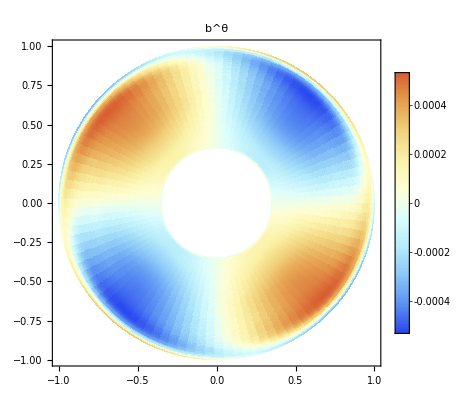

```mathematica
plot=EquatPlot[rj,ϕl,bθ,ColorFunction->"LightTemperatureMap",RegionFunction->Function[{x,y,z},First[Sprouts`domain]<Norm[{x,y}]<Last[Sprouts`domain]],PlotLegends->Placed[BarLegend[Automatic,LabelStyle->basestyle],After],BaseStyle->basestyle,PlotRange->All,PlotLabel->"b^θ",PlotTheme->"Detailed"]
```

```mathematica
plot=MeridPlot[rj,θk,br,0,ColorFunction->"LightTemperatureMap",RegionFunction->Function[{x,y,z},First[Sprouts`domain]<Norm[{x,y}]<Last[Sprouts`domain]],PlotLegends->Placed[BarLegend[Automatic,LabelStyle->basestyle],After],BaseStyle->basestyle,PlotRange->All,PlotLabel->"b^r",PlotTheme->"Detailed",AspectRatio->2]
```

-Graphics-